NSum::nsnum: Summand (or its derivative) (2 π^2 n^4 Exp[9 u]-3 π n^2 Exp[5 u]) Exp[-π n^2 Exp[4 u]] is not numerical at point n = 1.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

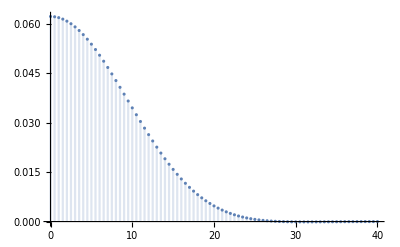

```mathematica
Infty := 8
phi[u_] := NSum[(2*Pi^2*n^4*Exp[9*u] - 3*Pi*n^2*Exp[5*u])*Exp[(-Pi)*n^2*Exp[4*u]], {n, 1, Infty}]
H[λ_, z_] := NIntegrate[Exp[λ*u^2]*phi[u]*Cos[z*u], {u, 0, Infty}]
DiscretePlot[H[0, z], {z, 0, 40, 0.5}]
```

```mathematica
(*Implementation using integration between 0 and 1*)
Infty:=10
phi[u_]:=NSum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, Infty}]
dH[l_, z_, t_]:=Exp[l*(t/(1-t))^2]*phi[t/(1-t)]*Cos[z *(t/(1-t))]/(1-t)^2
H[l_, z_]:=NIntegrate[dH[l, z, t], {t, 0, 1}]
Quiet[H[0, 2]]
```

0.0607197

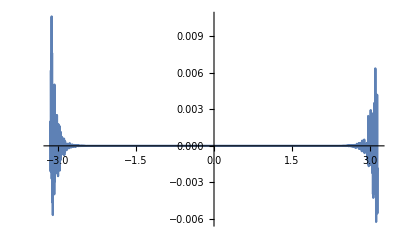

```mathematica
(*Implementation of integration between 0 and 1 using "General Midpoint Rule Formula" of atan function*)
f[theta_,x_]:=theta/(1+theta^2*x^2)
aTan[theta_,M_,nMax_]:=2*Sum[(Function[x,Evaluate[D[f[theta,x],{x,2*n}]]][(m-1/2)/M])/((2*n+1)!*(2*M)^(2*n+1)),{m,1,M},{n,0,nMax}]
Plot[{ArcTan[theta]-aTan[theta,1,30]},{theta,-Pi,Pi},PlotRange->All]
```

```mathematica
(*Implementation of integration between 0 and 1 using "General Midpoint Rule Formula" of H function*)
Infty:=4
phi[u_]:=Sum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, Infty}]
dH[l_, z_,t_]:=Exp[l*(t/(1-t))^2]*phi[t/(1-t)]*Cos[z*t/(1-t)]/(1-t)^2

(*General Midpoint Rule Formula*)
GMRF[l_, z_,M_,nMax_]:=2*Sum[(Function[x,Evaluate[D[dH[l, z,x],{x,2*n}]]][(m-1/2)/M])/((2*n+1)!*(2*M)^(2*n+1)),{m,1,M},{n,0,nMax}]

(*Fast integration to get values of H*)
H[l_, z_]:=NIntegrate[Exp[l*u^2]*phi[u]*Cos[z *u], {u, 0, Infty}]
DiscretePlot[H[0, 0]-GMRF[0, 0, 3, 5],{z, 0, 1, 0.1},PlotRange->All]
```

General::munfl: Exp[-1543.73] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2744.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.52419×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Infty:=4
phi[u_]:=Sum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, Infty}]
dH[z_,t_]:=phi[t/(1-t)]*Cos[z*t/(1-t)]/(1-t)^2

f16[z_, n_]:=Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][1/2])*((6z/5)^k*Cos[(k*Pi)/2+z/5])/(k!*(2n-k)!), {k, 0, 2n}]
f12[z_, n_]:=Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][1/6])*((2z)^k*Cos[(k*Pi)/2+z])/(k!*(2n-k)!), {k, 0, 2n}]
f56[z_, n_]:=Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][5/6])*((6z)^k*Cos[(k*Pi)/2+5*z])/(k!*(2n-k)!), {k, 0, 2n}]

Infty2:=5
H[z_]:=2*Sum[(f16[z, n]+f12[z, n]+f56[z, n])/(6^(2n+1)*(2n+1)), {n, 0, Infty2}]
```

```mathematica
Infty:=4
phi[u_]:=Sum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, Infty}]
dH[z_,t_]:=phi[t/(1-t)]*Cos[z*t/(1-t)]/(1-t)^2

f16c[z_, n_]:=Cos[z/5]*Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][1/6])*((6z/5)^k*Cos[(k*Pi)/2])/(k!*(2n-k)!*6^(2n+1)*(2n+1)), {k, 0, 2n}]
f16s[z_, n_]:=Sin[z/5]*Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][1/6])*((6z/5)^k*Sin[(k*Pi)/2])/(k!*(2n-k)!*6^(2n+1)*(2n+1)), {k, 0, 2n}]

f12c[z_, n_]:=Cos[z]*Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][1/2])*((2z)^k*Cos[(k*Pi)/2])/(k!*(2n-k)!*6^(2n+1)*(2n+1)), {k, 0, 2n}]
f12s[z_, n_]:=Sin[z]*Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][1/2])*((2z)^k*Sin[(k*Pi)/2])/(k!*(2n-k)!*6^(2n+1)*(2n+1)), {k, 0, 2n}]

f56c[z_, n_]:=Cos[5z]*Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][5/6])*((6z)^k*Cos[(k*Pi)/2])/(k!*(2n-k)!*6^(2n+1)*(2n+1)), {k, 0, 2n}]
f56s[z_, n_]:=Sin[5z]*Sum[(Function[t,Evaluate[D[phi[t/(1-t)]/(1-t)^2,{t,2*n-k}]]][5/6])*((6z)^k*Sin[(k*Pi)/2])/(k!*(2n-k)!*6^(2n+1)*(2n+1)), {k, 0, 2n}]

Infty2:=8
H[z_]:=2*Sum[(f16c[z, n]+f12c[z, n]+f56c[z, n]-f16s[z, n]-f12s[z, n]-f56s[z, n]), {n, 0, Infty2}]
N[H[2]]
```

General::munfl: Exp[-1543.73] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2744.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1543.73] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0603104

```mathematica
Func[u_]:=Exp[-Pi*n^2*Exp[4*u]]
D[Exp[f[x]], {u, k}]
```

0

D[Exp[f[u]], {u, k}]

WolframAlphaQueryResults

```mathematica
D[Exp[4*u*v], {u, k}]
```

4^k ⅇ^(4 u v) v^k

```mathematica
Sum[(-1)^u*Binomial[v, u]*(v - u)^k, {u, 0, v}]
```

v! StirlingS2[k,v]

Sum[StirlingS2[k, v]*(-Pi*k^2)^v, {v, 0, k}]

WolframAlphaQueryResults

Integrate[e^(λ*u^2)*ϕ[u]*Cos[z*u], {u, 0, Infinity}]

WolframAlphaQueryResults

```mathematica
Φ[u_]:=NSum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, Infinity}]
DeBruijnNewmanFunction[λ_, z_]:=NIntegrate[Exp[λ*u^2]*Φ[u]*Cos[z *u], {u, 0, Infinity}]
DeBruijnNewmanFunction[z_]:=NIntegrate[Φ[u]*Cos[z *u], {u, 0, Infinity}]
```

```mathematica
Plot[DeBruijnNewmanFunction[3,x+ⅈ], {x, 0, 10}]
```

NSum::nsnum: Summand (or its derivative) (2 π^2 n^4 Exp[9 u]-3 π n^2 Exp[5 u]) Exp[-π n^2 Exp[4 u]] is not numerical at point n = 46662.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

$Aborted